# Is an Adjacency Matrix sufficient as input for a Neural Network?

```mathematica
$Path=Prepend[$Path,NotebookDirectory[]];
<<DeepGraphDraw`
```

```mathematica
ds=MakeSimpleQDataset[1000, "NumberOfVertices"->200];
pd=PartitionData[ds, {0.7, 0.2, .1}];
```

```mathematica
Length[ds]
```

2000

```mathematica
inputDimension=Dimensions[First[First[ds]]];
```

```mathematica
cnn=NetInitialize@NetChain[
{
ConvolutionLayer[128,{3}, "PaddingSize"->1],
Tanh,
ConvolutionLayer[256,{3}, "PaddingSize"->1],
Ramp,
BatchNormalizationLayer[],
ConvolutionLayer[128,{3}],
Tanh,
ConvolutionLayer[64,{3}],
Ramp,
BatchNormalizationLayer[],
ConvolutionLayer[32,{3}],
Tanh,
ConvolutionLayer[10,{3}],
Tanh,
AggregationLayer[Mean],
LinearLayer[2],
SoftmaxLayer[]
},
"Input"-> inputDimension,
"Output"->NetDecoder[{"Class",{True,False}}]
]
```

NetChain[<>]

```mathematica
NetEncoder[{"Class",{True,False}}][Last[Last[ds]]]
(*NetDecoder[{"Class",{True,False}}][]*)
```

2

```mathematica
cnn[Normal[First[First[ds]]]]
```

True

```mathematica
tnetr=NetTrain[cnn,pd["TrainingData"],All,ValidationSet->pd["ValidationData"],TargetDevice->"CPU"];
```

```mathematica
tnetr
```

NetTrainResultsObject[<>]

## Look at Classifier Measurement

```mathematica
cm=ClassifierMeasurements[
tnetr["TrainedNet"],
Rule@@@Normal[pd["TestData"]]
]
```

ClassifierMeasurementsObject[…]

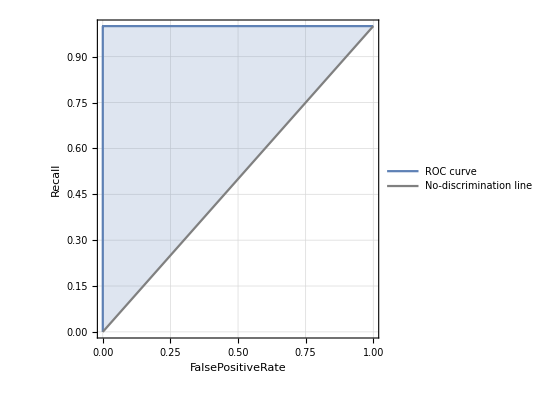
<|True→-Graphics-,False→-Graphics-|>

```mathematica
cm["ROCCurve"]
```